3430 ⅇ^(-25. (-5.69+ρ)^2)+1960 ⅇ^(-25. (-5.27+ρ)^2)

2536.41

743 ⅇ^(-156.25 (-5.6+ρ)^2)+1298 ⅇ^(-25. (-5.27+ρ)^2)

168.498

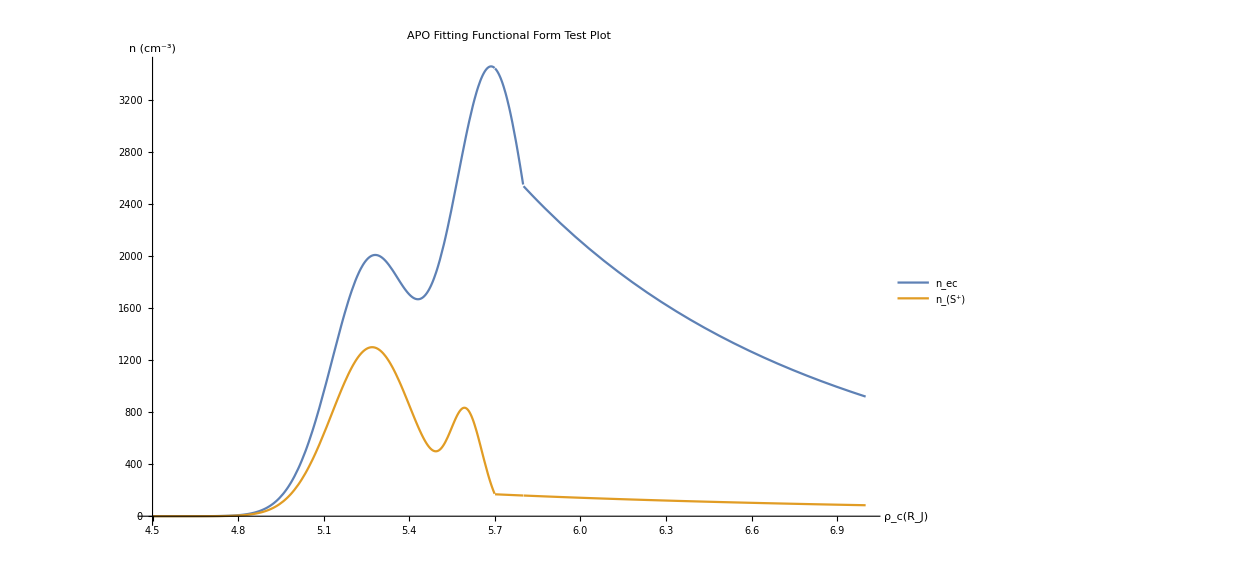

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

(*DUSK GUess to plug in to compare*)
ρcne=5.27;(*V1 Inbound cold torus nec peak density location*)
ρRne=5.69; (*V1 Inbound ribbon torus nec peak density location*)
ρOR=5.8;
A = 1960; (*V1 Inbound cold torus nec peak density*)
B =0.2 ;
 Χ=3430; (*V1 Inbound riboon torus nec peak density*)
Δ = 0.2; 
F = 5.4; (*Steffl2004b*)

necin[ρ_] = A*Exp[-((ρ-ρcne)/B)^2] + Χ*Exp[-((ρ-ρRne)/Δ)^2]
Ε = necin[ρOR]
necout[ρ_] =Ε*(ρ/ρOR)^-F;

nec[ρ_] = Piecewise[{{necin[ρ] ,ρ<ρOR},{necout[ρ] ,ρ>=ρOR}}];
(*Now for S^+*)

ρcnsp=5.27;(*V1 Inbound cold torus nec peak density location*)
ρRnsp=5.60; (*V1 Inbound ribbon torus nec peak density location*)
ρORsp=5.7;
G= 1298; (*V1 Inbound cold torus nec peak density*)
H =0.2 ;
 Ι=743; (*V1 Inbound riboon torus nec peak density*)
J = 0.08; 
L = 3.37; (*My fits Cassin UVIS*)

nspin[ρ_] = G*Exp[-((ρ-ρcnsp)/H)^2] + Ι*Exp[-((ρ-ρRnsp)/J)^2]
Κ= nspin[ρORsp]
nspout[ρ_] =Κ*(ρ/ρORsp)^-L;
nsp[ρ_] = Piecewise[{{nspin[ρ] ,ρ<ρORsp},{nspout[ρ] ,ρ>=ρORsp}}];
Plot[{nec[ρ],nsp[ρ]},{ρ,4.5,7},AxesLabel->{"ρ_c(R_J)","n (cm^-3)"},PlotLabel->"APO Fitting Functional Form Test Plot",PlotLegends->{"n_ec","n_(S^+)"}]
```

```mathematica
necout[6]
nspout[6]
```

2112.1

141.75